# TSM-Growth

```mathematica
ClearAll["Global`*"]
```

## Aufstellen der Gleichungen

```mathematica
fQW[𝕙g_,𝕙gn_,𝕙gdot_,tt_]:=Block[{}
,

ϕ ={𝕙g⟦1⟧,𝕙g⟦2⟧,𝕙g⟦3⟧,𝕙g⟦4⟧};
ϕn ={𝕙gn⟦1⟧,𝕙gn⟦2⟧,𝕙gn⟦3⟧,𝕙gn⟦4⟧};
ϕdot ={𝕙gdot⟦1⟧,𝕙gdot⟦2⟧,𝕙gdot⟦3⟧,𝕙gdot⟦4⟧};
ϕ0 =𝕙g⟦5⟧;
ϕ0n =𝕙gn⟦5⟧;
ϕ0dot =𝕙gdot⟦5⟧;
ψ ={𝕙g⟦6⟧,𝕙g⟦7⟧,𝕙g⟦8⟧,𝕙g⟦9⟧};
ψn={𝕙gn⟦6⟧,𝕙gn⟦7⟧,𝕙gn⟦8⟧,𝕙gn⟦9⟧};
ψdot ={𝕙gdot⟦6⟧,𝕙gdot⟦7⟧,𝕙gdot⟦8⟧,𝕙gdot⟦9⟧};
γ=𝕙g⟦10⟧;
Φ={ϕ⟦1⟧ψ⟦1⟧,ϕ⟦2⟧ψ⟦2⟧,ϕ⟦3⟧ψ⟦3⟧,ϕ⟦4⟧ψ⟦4⟧};
Φdot=Table[ϕdot⟦i⟧ψ⟦i⟧+ϕ⟦i⟧ψdot⟦i⟧,{i,4}];

𝔸=-1/2({{a11, a12, a13, a14}, {a12, a22, a23, a24}, {a13, a23, a33, a34}, {a14, a24, a34, a44}});
𝔹=-1/2({{b11, 0, 0, 0}, {0, b22, 0, 0}, {0, 0, b33, 0}, {0, 0, 0, b44}});


(*Penalty=Kp1(1/(ϕ⟦1⟧^2(1-ϕ⟦1⟧)^2)+1/(ϕ⟦2⟧^2(1-ϕ⟦2⟧)^2)+1/(ϕ⟦3⟧^2(1-ϕ⟦3⟧)^2)+1/(ϕ⟦4⟧^2(1-ϕ⟦4⟧)^2)+1/(ψ⟦1⟧^2(1-ψ⟦1⟧)^2)+1/(ψ⟦2⟧^2(1-ψ⟦2⟧)^2)+1/(ψ⟦3⟧^2(1-ψ⟦3⟧)^2)+1/(ψ⟦4⟧^2(1-ψ⟦4⟧)^2)+1/(ϕ0^2(1-ϕ0)^2));

(*Lagrangian  of the holistic system*)
ℋ=c Φ.𝔸.Φ-α ψ.𝔹.ψ+Penalty+γ(Sum[ϕ⟦i⟧,{i,4}]+ϕ0-1.);*)
Penalty1=η1 Kp1(1/(ϕ⟦1⟧^2(1-ϕ⟦1⟧)^2));
Penalty2=η2 Kp1(1/(ϕ⟦2⟧^2(1-ϕ⟦2⟧)^2));
Penalty3=η3 Kp1(1/(ϕ⟦3⟧^2(1-ϕ⟦3⟧)^2));
Penalty4=η4 Kp1(1/(ϕ⟦4⟧^2(1-ϕ⟦4⟧)^2));
Penalty5=η1 Kp1(1/(ψ⟦1⟧^2(1-ψ⟦1⟧)^2));
Penalty6=η2 Kp1(1/(ψ⟦2⟧^2(1-ψ⟦2⟧)^2));
Penalty7=η3 Kp1(1/(ψ⟦3⟧^2(1-ψ⟦3⟧)^2));
Penalty8=η4 Kp1(1/(ψ⟦4⟧^2(1-ψ⟦4⟧)^2));
Penalty9=Kp1(1/(ϕ0^2(1-ϕ0)^2));
ℋ=c[tt] Φ.𝔸.Φ-α[tt] ψ.𝔹.ψ+Penalty1+Penalty2+Penalty3+Penalty4+Penalty5+Penalty6+Penalty7+Penalty8+Penalty9+ γ(Sum[ϕ⟦i⟧,{i,4}]+ ϕ0-1.);
η=({{η1, 0, 0, 0}, {0, η2, 0, 0}, {0, 0, η3, 0}, {0, 0, 0, η4}});
ηϕ=({{ηϕ1, 0, 0, 0}, {0, ηϕ2, 0, 0}, {0, 0, ηϕ3, 0}, {0, 0, 0, ηϕ4}});
Δrd=1/2 Φdot.η.Φdot+1/2 ϕdot.ηϕ.ϕdot;
Δ0= 1/2 ϕ0dot^2;

(*here a time dependent term can be added*)

ℚϕ=Table[D[ℋ,ϕ⟦i⟧] +D[Δrd,ϕdot⟦i⟧] ,{i,4}];
ℚψ=Table[D[ℋ,ψ⟦i⟧] +D[Δrd,ψdot⟦i⟧] ,{i,4}];
ℚϕ0=D[ℋ,ϕ0]+D[Δ0,ϕ0dot];
ℚγγ=D[ℋ,γ];
(*Total[ϕ]+ϕ0-1;*)


Return[{ℚϕ⟦1⟧,ℚϕ⟦2⟧,ℚϕ⟦3⟧,ℚϕ⟦4⟧,ℚϕ0,ℚψ⟦1⟧,ℚψ⟦2⟧,ℚψ⟦3⟧,ℚψ⟦4⟧,ℚγγ}];

]
vd={vd1,vd2,vd3,vd4,vd5,vd6,vd7,vd8,vd9,vd10};
v={v1,v2,v3,v4,v5,v6,v7,v8,v9,v10};
vn={v1n,v2n,v3n,v4n,v5n,v6n,v7n,v8n,v9n,v10n};
exp=fQW[v,vn,vd,te];
exp//Simplify;
exp⟦1⟧ = ReplaceAll[exp⟦1⟧,exp⟦1⟧->  exp⟦1⟧/η1]//Simplify;
exp⟦2⟧ = ReplaceAll[exp⟦2⟧,exp⟦2⟧->  exp⟦2⟧/η2]//Simplify;
exp⟦3⟧ = ReplaceAll[exp⟦3⟧,exp⟦3⟧->  exp⟦3⟧/η3]//Simplify;
exp⟦4⟧ = ReplaceAll[exp⟦4⟧,exp⟦4⟧->  exp⟦4⟧/η4]//Simplify;
exp⟦6⟧ = ReplaceAll[exp⟦6⟧,exp⟦6⟧->  exp⟦6⟧/η1]//Simplify;
exp⟦7⟧ = ReplaceAll[exp⟦7⟧,exp⟦7⟧->  exp⟦7⟧/η2]//Simplify;
exp⟦8⟧ = ReplaceAll[exp⟦8⟧,exp⟦8⟧->  exp⟦8⟧/η3]//Simplify;
exp⟦9⟧ = ReplaceAll[exp⟦9⟧,exp⟦9⟧->  exp⟦9⟧/η4]//Simplify;
exp⟦1⟧ = ReplaceAll[exp⟦1⟧,a-> xy]//Simplify;
exp//Simplify
myrul1=Table[vd⟦i⟧-> (v⟦i⟧-vn⟦i⟧)/dt,{i,1,10}];
Eq=Simplify[ReplaceAll[exp,myrul1]];
𝕂=Table[D[Eq⟦i⟧,{v}],{i,1,10}];
```

{(Kp1 (2-4 v1))/((-1+v1)^3 v1^3)+(v10+v6^2 vd1 η1+v1 v6 vd6 η1+vd1 ηϕ1)/η1-(v6 (a11 v1 v6+a12 v2 v7+a13 v3 v8+a14 v4 v9) c[te])/η1,(Kp1 (2-4 v2))/((-1+v2)^3 v2^3)+(v10+v7^2 vd2 η2+v2 v7 vd7 η2+vd2 ηϕ2)/η2-(v7 (a12 v1 v6+a22 v2 v7+a23 v3 v8+a24 v4 v9) c[te])/η2,(Kp1 (2-4 v3))/((-1+v3)^3 v3^3)+(v10+v8^2 vd3 η3+v3 v8 vd8 η3+vd3 ηϕ3)/η3-(v8 (a13 v1 v6+a23 v2 v7+a33 v3 v8+a34 v4 v9) c[te])/η3,(Kp1 (2-4 v4))/((-1+v4)^3 v4^3)+(v10+v9^2 vd4 η4+v4 v9 vd9 η4+vd4 ηϕ4)/η4-(v9 (a14 v1 v6+a24 v2 v7+a34 v3 v8+a44 v4 v9) c[te])/η4,v10+(Kp1 (2-4 v5))/((-1+v5)^3 v5^3)+vd5,-(2 Kp1)/((-1+v6)^2 v6^3)-(2 Kp1)/((-1+v6)^3 v6^2)+v1 v6 vd1+v1^2 vd6-(v1 (a11 v1 v6+a12 v2 v7+a13 v3 v8+a14 v4 v9) c[te])/η1+(b11 v6 α[te])/η1,-(2 Kp1)/((-1+v7)^2 v7^3)-(2 Kp1)/((-1+v7)^3 v7^2)+v2 v7 vd2+v2^2 vd7-(v2 (a12 v1 v6+a22 v2 v7+a23 v3 v8+a24 v4 v9) c[te])/η2+(b22 v7 α[te])/η2,-(2 Kp1)/((-1+v8)^2 v8^3)-(2 Kp1)/((-1+v8)^3 v8^2)+v3 v8 vd3+v3^2 vd8-(v3 (a13 v1 v6+a23 v2 v7+a33 v3 v8+a34 v4 v9) c[te])/η3+(b33 v8 α[te])/η3,-(2 Kp1)/((-1+v9)^2 v9^3)-(2 Kp1)/((-1+v9)^3 v9^2)+v4 v9 vd4+v4^2 vd9-(v4 (a14 v1 v6+a24 v2 v7+a34 v3 v8+a44 v4 v9) c[te])/η4+(b44 v9 α[te])/η4,-1.+v1+v2+v3+v4+v5}

## Varibalendefinition

```mathematica
(*Dateiname für die Ausgabe*)
dateiname = "AusgabeFall01-changing";
txt =".txt";
dat = ".dat";
dataDateiname=StringJoin[dateiname,dat];
varDateiname=StringJoin[dateiname,txt];
(*Interaktionsvariablen*)
(*a11=2;
a12=1;
a13=1;
a14=1;
a22=2;
a23=1;
a24=1;
a33=2;
a34=1;
a44=2;*)
a11=1;
a12=5;
a13=5;
a14=5;
a22=1;
a23=3;
a24=3;
a33=1;
a34=2;
a44=1;
(*Antibiotikavariablen*)
b11=0.4;
b22=0.3;
b33=0.2;
b44=0.1;
(*Viskositäten*)
(*η1=1;
η2=1.5;
η3=3;
η4=5;*)
η1=0.8;
η2=1;
η3=1.5;
η4=2;

ηϕ1=η1;
ηϕ2=η2;
ηϕ3=η3;
ηϕ4=η4;
(*Penalty Parameter*)
Kp1= 10^-4;
(*Initiale Bedingungen*)
{ϕ1i,ϕ2i,ϕ3i,ϕ4i}={0.02,0.02,0.02,0.02};
ϕ5i=1-(ϕ1i+ϕ2i+ϕ3i+ϕ4i);
(*Numerische Parameter*)
one=0.999;
err=1;
eps=10^-3;
maxtimestep =1500;
dt=10^-4;
s=5;
(*Menge an Antibiotika*)
α[t_]:=10;
(*Piecewise[{{100,t>500 dt}},0];*)
(*Menge an Nährstoffen*)
c[t_]:=50+50Sin[500 t];
(*100;
c[t_]:=100t;*)

exp//Simplify
```

{(1-2 v1)/(5000 (-1+v1)^3 v1^3)+1.25 (v10+(0.8+0.8 v6^2) vd1+0.8 v1 v6 vd6)-62.5 v6 (v1 v6+5. v2 v7+5. v3 v8+5. v4 v9) (1.+Sin[500 te]),v10+(1-2 v2)/(5000 (-1+v2)^3 v2^3)+vd2+v7^2 vd2+v2 v7 vd7-50 v7 (5 v1 v6+v2 v7+3 v3 v8+3 v4 v9) (1+Sin[500 te]),(1-2 v3)/(5000 (-1+v3)^3 v3^3)+0.666667 (v10+(1.5+1.5 v8^2) vd3+1.5 v3 v8 vd8)-33.3333 v8 (5. v1 v6+3. v2 v7+v3 v8+2. v4 v9) (1.+Sin[500 te]),v10/2+(1-2 v4)/(5000 (-1+v4)^3 v4^3)+vd4+v9^2 vd4+v4 v9 vd9-25 v9 (5 v1 v6+3 v2 v7+2 v3 v8+v4 v9) (1+Sin[500 te]),v10-1/(5000 (-1+v5)^2 v5^3)-1/(5000 (-1+v5)^3 v5^2)+vd5,-1/(5000 (-1+v6)^2 v6^3)-1/(5000 (-1+v6)^3 v6^2)+5. v6+v1 v6 vd1+v1^2 vd6-62.5 v1 (v1 v6+5. v2 v7+5. v3 v8+5. v4 v9) (1.+Sin[500 te]),-1/(5000 (-1+v7)^2 v7^3)-1/(5000 (-1+v7)^3 v7^2)+3. v7+v2 v7 vd2+v2^2 vd7-50 v2 (5 v1 v6+v2 v7+3 v3 v8+3 v4 v9) (1+Sin[500 te]),-1/(5000 (-1+v8)^2 v8^3)-1/(5000 (-1+v8)^3 v8^2)+1.33333 v8+v3 v8 vd3+v3^2 vd8-33.3333 v3 (5. v1 v6+3. v2 v7+v3 v8+2. v4 v9) (1.+Sin[500 te]),-1/(5000 (-1+v9)^2 v9^3)-1/(5000 (-1+v9)^3 v9^2)+0.5 v9+v4 v9 vd4+v4^2 vd9-25 v4 (5 v1 v6+3 v2 v7+2 v3 v8+v4 v9) (1+Sin[500 te]),-1.+v1+v2+v3+v4+v5}

## Speichern der Variablen

```mathematica
SaveVariableState[variableName_String,value_,filePath_String]:=Module[{currentData,formattedEntry},
(*Lese vorhandene Daten aus der Datei,falls vorhanden*)
currentData=If[FileExistsQ[filePath],Import[filePath,"Text"],""];
(*Neue Variable hinzufügen oder vorhandenen Wert aktualisieren*)
formattedEntry=variableName<>" = "<>ToString[value];
(*Sicherstellen,dass ein Zeilenumbruch existiert*)
currentData=If[StringLength[currentData]>0&&!StringEndsQ[currentData,"\n"],currentData<>"\n",currentData];
(*Daten schreiben*)
Export[filePath,currentData<>formattedEntry<>"\n","Text"];
(*Rückgabe des Werts,damit er weiterhin nutzbar bleibt*)
value];
ahat11 = a11/η1;
ahat12 = a12/η1;
ahat13 = a13/η1;
ahat14 = a14/η1;
ahat21 = a12/η2;
ahat22 = a22/η2;
ahat23 = a23/η2;
ahat24 = a24/η2;
ahat31 = a13/η3;
ahat32 = a23/η3;
ahat33 = a33/η3;
ahat34 = a34/η3;
ahat41 = a14/η4;
ahat42 = a24/η4;
ahat43 = a34/η4;
ahat44 = a44/η4;
SaveVariableState["maxtimestep",maxtimestep,varDateiname];
SaveVariableState["dt",dt,varDateiname];

SaveVariableState["ahat11",ahat11,varDateiname];
SaveVariableState["ahat12",ahat12,varDateiname];
SaveVariableState["ahat13",ahat13,varDateiname];
SaveVariableState["ahat14",ahat14,varDateiname];

SaveVariableState["ahat21",ahat21,varDateiname];
SaveVariableState["ahat22",ahat22,varDateiname];
SaveVariableState["ahat23",ahat23,varDateiname];
SaveVariableState["ahat24",ahat24,varDateiname];

SaveVariableState["ahat31",ahat31,varDateiname];
SaveVariableState["ahat32",ahat32,varDateiname];
SaveVariableState["ahat33",ahat33,varDateiname];
SaveVariableState["ahat34",ahat34,varDateiname];

SaveVariableState["ahat41",ahat41,varDateiname];
SaveVariableState["ahat42",ahat42,varDateiname];
SaveVariableState["ahat43",ahat43,varDateiname];
SaveVariableState["ahat44",ahat44,varDateiname];

SaveVariableState["a11",a11,varDateiname];
SaveVariableState["a12",a12,varDateiname];
SaveVariableState["a13",a13,varDateiname];
SaveVariableState["a14",a14,varDateiname];
SaveVariableState["a22",a22,varDateiname];
SaveVariableState["a23",a23,varDateiname];
SaveVariableState["a24",a24,varDateiname];
SaveVariableState["a33",a33,varDateiname];
SaveVariableState["a34",a34,varDateiname];
SaveVariableState["a44",a44,varDateiname];

SaveVariableState["b11",b11,varDateiname];
SaveVariableState["b22",b22,varDateiname];
SaveVariableState["b33",b33,varDateiname];
SaveVariableState["b44",b44,varDateiname];

SaveVariableState["η1",η1,varDateiname];
SaveVariableState["η2",η2,varDateiname];
SaveVariableState["η3",η3,varDateiname];
SaveVariableState["η4",η4,varDateiname];

SaveVariableState["Kp1",Kp1,varDateiname];

SaveVariableState["c",c,varDateiname];
SaveVariableState["α",α,varDateiname];

SaveVariableState["ϕ1i",ϕ1i,varDateiname];
SaveVariableState["ϕ2i",ϕ2i,varDateiname];
SaveVariableState["ϕ3i",ϕ3i,varDateiname];
SaveVariableState["ϕ4i",ϕ4i,varDateiname];
SaveVariableState["ϕ5i",ϕ5i,varDateiname];
```

## Newton-Raphson

```mathematica
cc={};
myeror={};
myDetK={};
myConditioning = {};
νi={ϕ1i,ϕ2i,ϕ3i,ϕ4i,1-(ϕ1i+ϕ2i+ϕ3i+ϕ4i),one,one,one,one,eps};
ν0={eps,eps,eps,eps,one,one,one,one,one,0};

monitor1={{ϕ1i},{ϕ2i},{ϕ3i},{ϕ4i},{1-(ϕ1i+ϕ2i+ϕ3i+ϕ4i)},{one},{one},{one},{one},{1}};
monitor2={{ϕ1i},{ϕ2i},{ϕ3i},{ϕ4i}};
ta = 0;
monitor3={{N[c[0]]},{N[α[0]]}};
increment=0;
Do[
ta = ta+dt;
counter=0;
While[((err>eps)&& (counter<100)),
myrul2=Table[vn⟦i⟧->νi⟦i⟧,{i,1,10}];
myrul3=Append[Table[v⟦i⟧->ν0⟦i⟧,{i,1,10}],{te->ta}];
myrul23=Flatten[Append[myrul2,myrul3]];
𝕂N=ReplaceAll[𝕂,myrul23];
EqN=ReplaceAll[Eq,myrul23];
δν=-Inverse[𝕂N].EqN;
conditioning = LinearAlgebra`Private`MatrixConditionNumber[𝕂N];
AppendTo[myConditioning,conditioning];
ν0=ν0+δν;
err=δν.δν;
counter=counter+1;
AppendTo[cc,counter];
AppendTo[myeror,err];
];
Do[AppendTo[monitor1⟦i⟧,ν0⟦i⟧],{i,1,9}];
AppendTo[monitor1⟦10⟧,Total[ν0⟦1;;5⟧]];
Do[AppendTo[monitor2⟦i⟧,ν0⟦i⟧ν0⟦i+5⟧],{i,1,4}];
AppendTo[monitor3⟦1⟧,N[c[ta]]];
AppendTo[monitor3⟦2⟧,N[α[ta]]];
detK=Det[𝕂N];
AppendTo[myDetK,detK];
err=1;
νi=ν0;
increment=increment+1;
,{t,0,maxtimestep,1}]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.0042×10^8,-327.463,-327.463,-327.463,0.,-370.744,-0.32779,-0.32779,-0.32779,1.25},{-261.97,6.0042×10^8,-157.182,-157.182,0.,-0.262232,-370.312,-0.157339,-0.157339,1.},«7»,{1.,1.,1.,1.,1.,0.,0.,0.,0.,0.}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{3.63514×10^11,-327.244,-327.244,-327.244,0.,-394.123,-0.140269,-0.239229,-0.288709,1.25},{-261.795,1.78742×10^10,-157.077,-157.077,0.,-0.0528401,-386.994,-0.11483,-0.13858,1.},«7»,{1.,1.,1.,1.,1.,0.,0.,0.,0.,0.}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.15009×10^11,-326.953,-326.953,-326.953,0.,-392.168,-0.18697,-0.318986,-0.385049,1.25},{-261.562,5.65274×10^9,-156.937,-156.937,0.,-0.0704242,-382.667,-0.153113,-0.184823,1.},«7»,{1.,1.,1.,1.,1.,0.,0.,0.,0.,0.}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

## Ausgabe

-Graphics-

-Graphics-

-Graphics-

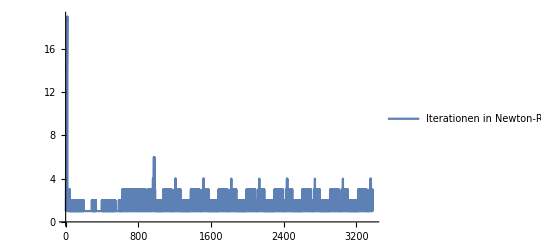

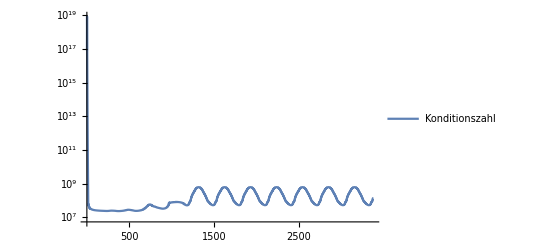

```mathematica
ListLinePlot[monitor1,PlotRange->All,PlotLegends->{"ϕ1","ϕ2","ϕ3","ϕ4","ϕ5 (Empty space)","ψ1","ψ2","ψ3","ψ4","Sum(ϕ1+ϕ2+ϕ3+ϕ4+ϕ5)"},PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick],Directive[Yellow,Thick],Directive[Green,Thick],Directive[Black,Thick],Directive[Red,Dashed],Directive[Blue,Dashed],Directive[Yellow,Dashed],Directive[Green,Dashed],Directive[Orange,Thick]},PlotMarkers->{" " ," " ," " ," " , " ", " "," " ," " ," " ," "}]
ListLinePlot[monitor2,PlotRange->All,PlotLegends->{"ϕ1ψ1","ϕ2ψ2","ϕ3ψ3","ϕ4ψ4"},PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick],Directive[Yellow,Thick],Directive[Green,Thick]},PlotMarkers->{"" ,"" ,"" ,"" }]
ListLinePlot[monitor3,PlotRange->All,PlotLegends->{"c","α"},PlotStyle->{Directive[Green,Thick],Directive[Red,Thick]},PlotMarkers->{"" ,"" }]
ListLinePlot[cc,PlotRange->All,PlotLegends->{"Iterationen in Newton-Raphson"}]
ListLinePlot[myConditioning,PlotRange->All,PlotLegends->{"Konditionszahl"},ScalingFunctions->{"Linear","Log"}]
```

## Speichern der Ergebnisse

```mathematica
(*Kombinierte Liste der Vektoren als zusätzliche Spalten*)
alleVektoren=Join[monitor1,monitor2,monitor3];
alleVektorenT = Transpose[alleVektoren];
(*Erstelle einen Vektor von 1 bis zur Anzahl der Zeilen*)
nummerierung=Range[Length[alleVektorenT]];

(*Füge den Nummerierungs-Vektor in die erste Spalte ein*)
alleVektorenMitNummerierung=MapThread[Prepend,{alleVektorenT,nummerierung}];

(*Spaltennamen hinzufügen*)
datenMitHeader=Prepend[alleVektorenMitNummerierung,{"timestep","phi1","phi2","phi3","phi4","phi0","psi1","psi2","psi3","psi4","Sum(phis)","phi1psi1","phi2psi2","phi3psi3","phi4psi4","c","alpha"}];

(*Speichern der kombinierten Vektoren in der Datei*)
Export[dataDateiname,datenMitHeader,"Table"];

(*Ausgabe des Dateipfads*)
Print["Die Vektoren wurden mit Nummerierung und Header in die Datei gespeichert: ",FileNameJoin[{Directory[],dataDateiname}]];
```

Die Vektoren wurden mit Nummerierung und Header in die Datei gespeichert: C:\Users\klempt\Documents\AusgabeFall01-changing.dat